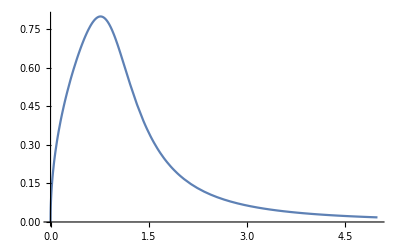

```mathematica
Clear["Global`*"];
g[x_]=x^(1/2)(x^6+1)^(-1/2);
Plot[g[x],{x,0,5},PlotRange->All]
```

```mathematica
Clear[x,α]
α=0.5;
x=4;xs={};
For[i1=1,i1≤200,i1++,
x=x+α g'[x];
AppendTo[xs,x];
];
```

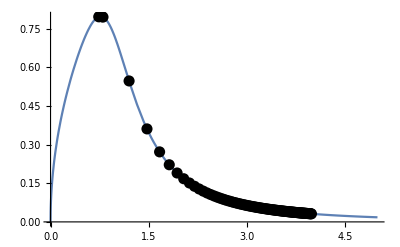

```mathematica
Clear[x]
Plot[g[x],{x,0,5},Epilog->{PointSize[0.02],Point[Table[{xs⟦i1⟧,g[xs⟦i1⟧]},{i1,1,Length[xs]}]]}]
```

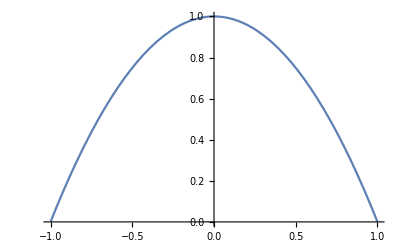

```mathematica
Clear["Global`*"];
g[x_]=1-x^2;
Plot[g[x],{x,-1,1},PlotRange->All]
```

```mathematica
Clear[x,α]
α=0.25;
x=0.94;xs={x};
For[i1=1,i1≤400,i1++,
x=x+α g'[x];
AppendTo[xs,x];
];
```

```mathematica
g[xs]//Chop
```

{0.1164,0.7791,0.944775,0.986194,0.996548,0.999137,0.999784,0.999946,0.999987,0.999997,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

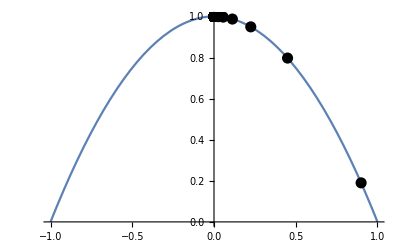

```mathematica
Clear[x]
Plot[g[x],{x,-1,1},Epilog->{PointSize[0.02],Point[Table[{xs⟦i1⟧,g[xs⟦i1⟧]},{i1,1,Length[xs]}]]}]
```